```mathematica
x=Table[10+5*i,{i,0,4}]
y={27.0,26.8,26.5,26.3,26.1}
xy=Table[{x[[i]],y[[i]]},{i,1,5}]

q[a_,b_,c_]:=Sum[(a+b*x[[i]]+c*x[[i]]*x[[i]]-y[[i]])^2,{i,1,5}]
NSolve[{D[q[a,b,c],a]==0,D[q[a,b,c],b]==0,D[q[a,b,c],c]==0},{a,b,c}]
```

{{a→27.56,b→-0.0574286,c→0.000285714}}

```mathematica
aa=27.560000000000006;bb=-0.05742857142857273;cc=0.00028571428571432965;
```

```mathematica
f[x_]:=aa+bb*x+cc*x*x
```

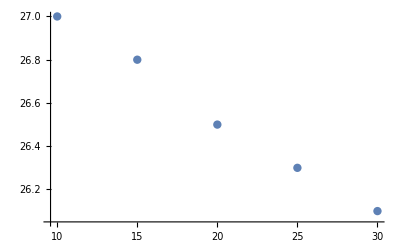

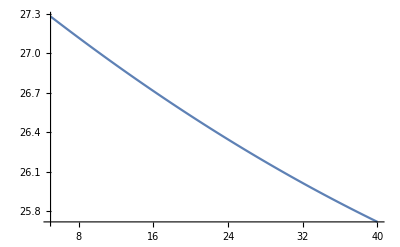

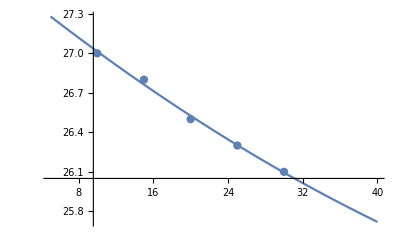

```mathematica
t1=ListPlot[xy,PlotStyle->PointSize[0.015]]
t2=Plot[f[x],{x,5,40},PlotRange->All]
Show[t1,t2,PlotRange->All]
```